```mathematica
Quit[];
```

```mathematica
MR=1;
m0=0.55;
mu=1;
y0=4π √0.1 m0;
Γ0=0.2;
```

```mathematica
LogDeltaInvInt[s_,m_]:=-(√(4 m^2-s))/(√-s)  (Log[1+√(s/(s-4 m^2))]-Log[1-√(s/(s-4 m^2))])+2-2 Log[m];

DeltaInvInt[s_,m_]:=-1/s+(√-s)/(√(4 m^2-s))((2 m^2)/s^2(  Log[1-√(s/(-4 m^2+s))]-Log[1+√(s/(-4 m^2+s))]));
f[s_,m_,μ_,y_]:=y^2/(16 π^2)(LogDeltaInvInt[s,m]+2Log[μ]);
fPrime[s_,m_,μ_,y_]:=y^2/(16 π^2)(DeltaInvInt[s,m]);
```

```mathematica
(*MSbar Mass and Width*)
MMSbar[M_,m_,μ_,y_,Γ_]:=Sqrt[M^2+Re[f[M^2-ⅈ×M×Γ,m,μ,y]]];
Mbare=MMSbar[MR,m0,mu,y0,Γ0]
GammaMSbar[M_,m_,μ_,y_,Γ_]:=M/MMSbar[M,m,μ,y,Γ] Γ(1+Re[fPrime[M^2-ⅈ×M×Γ,m,μ,y]]);
Gammabare=GammaMSbar[MR,m0,mu,y0,Γ0]
```

1.03049

0.202375

```mathematica
(*Pole Mass*)
Sqrt[Mbare^2-ⅈ Mbare Gammabare-f[Mbare^2-ⅈ×Mbare×Gammabare,m0,mu,y0]]
Sqrt[MR^2-ⅈ MR Γ0]
MPole[M_,m_,μ_,y_,Γ_]:=Sqrt[M^2-ⅈ M Γ-ⅈ Im[f[M^2-ⅈ M Γ,m,μ,y]]-ⅈ M Γ Re[fPrime[M^2-ⅈ M Γ,m,μ,y]]];
Mp=MPole[MR,m0,mu,y0,Γ0]
```

1.00353-0.0974765 ⅈ

1.00494-0.0995085 ⅈ

1.00483-0.0984354 ⅈ

```mathematica
(*Pole Residue*)
ResMSbar[M_,m_,μ_,y_,Γ_]:=1-fPrime[M^2-ⅈ×M×Γ,m,μ,y];
ZMSbar=ResMSbar[Mbare,m0,mu,y0,Γ0]
ResOS[M_,m_,μ_,y_,Γ_]:=1-ⅈ Im[fPrime[M^2-ⅈ×M×Γ,m,μ,y]];
ZOS=ResOS[MR,m0,mu,y0,Γ0]
```

0.956398+0.033563 ⅈ

1.+0.0252542 ⅈ

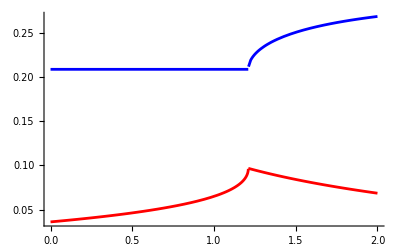

```mathematica
SigmaMSbar[s_,M_,m_,μ_,y_,Γ_]:=ⅈ×M×Γ+f[s,m,μ,y];
Show[Plot[Re[SigmaMSbar[s,Mbare,m0,mu,y0,Gammabare]],{s,0,2},PlotStyle->{Red},MaxRecursion->10],Plot[Im[SigmaMSbar[s,Mbare,m0,mu,y0,Gammabare]],{s,0,2},PlotStyle->{Blue},MaxRecursion->10],PlotRange->Full,AxesOrigin->{0,0}]
```

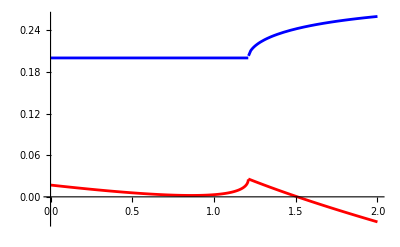

```mathematica
SigmaOS[s_,M_,m_,μ_,y_,Γ_]:=ⅈ×M×Γ+f[s,m,μ,y]-Re[f[M^2-ⅈ×M×Γ,m,μ,y]]-(s-M^2)Re[fPrime[M^2-ⅈ×M×Γ,m,μ,y]];
Show[Plot[Re[SigmaOS[s,MR,m0,mu,y0,Γ0]],{s,0,2},PlotStyle->{Red},MaxRecursion->10],Plot[Im[SigmaOS[s,MR,m0,mu,y0,Γ0]],{s,0,2},PlotStyle->{Blue},MaxRecursion->10],PlotRange->Full,AxesOrigin->{0,0}]
```

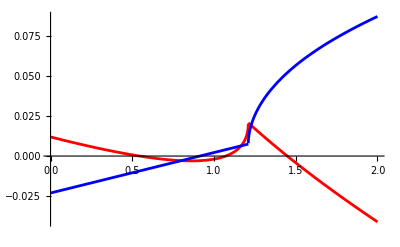

```mathematica
SigmaCOS[s_,M_,m_,μ_,y_]:=f[s,m,μ,y]-f[M^2,m,μ,y]-(s-M^2)fPrime[M^2,m,μ,y];
Show[Plot[Re[SigmaCOS[s,Sqrt[MR^2-ⅈ MR Γ0],m0,mu,y0]],{s,0,2},PlotStyle->{Red},MaxRecursion->10],Plot[Im[SigmaCOS[s,Sqrt[MR^2-ⅈ MR Γ0],m0,mu,y0]],{s,0,2},PlotStyle->{Blue},MaxRecursion->10],PlotRange->Full,AxesOrigin->{0,0}]
```

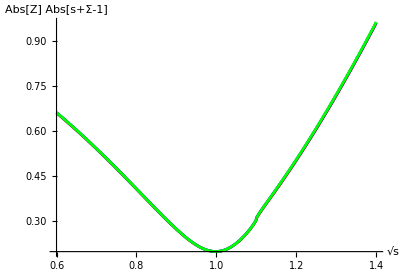

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[ZMSbar]Abs[s-Mbare^2+SigmaMSbar[s,Mbare,m0,mu,y0,Gammabare]]},{s,0.36,1.96},PlotStyle->{Red},MaxRecursion->10],ParametricPlot[{Sqrt[s],Abs[ZOS]Abs[s-MR^2+SigmaOS[s,MR,m0,mu,y0,Γ0]]},{s,0.36,1.96},PlotStyle->{Blue},MaxRecursion->10],ParametricPlot[{Sqrt[s],Abs[s-Mp^2+SigmaCOS[s,Sqrt[MR^2-ⅈ MR Γ0],m0,mu,y0]]},{s,0.36,1.96},PlotStyle->{Green},MaxRecursion->10],AspectRatio->0.7,AxesLabel->{Sqrt[s],Abs[Z]Abs[s-1+Σ]}]
```

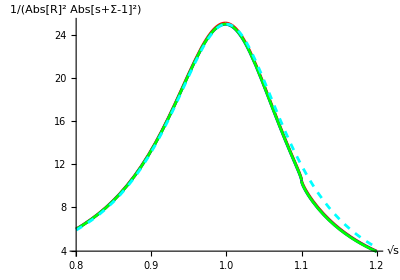

```mathematica
Show[ParametricPlot[{Sqrt[s],(Abs[ZMSbar]Abs[s-Mbare^2+SigmaMSbar[s,Mbare,m0,mu,y0,Gammabare]])^-2},{s,0.64,1.44},PlotStyle->{Red},MaxRecursion->10],ParametricPlot[{Sqrt[s],(Abs[ZOS]Abs[s-MR^2+SigmaOS[s,MR,m0,mu,y0,Γ0]])^-2},{s,0.64,1.44},PlotStyle->{Blue},MaxRecursion->10],ParametricPlot[{Sqrt[s],(Abs[s-Mp^2+SigmaCOS[s,Sqrt[MR^2-ⅈ MR Γ0],m0,mu,y0]])^-2},{s,0.64,1.44},PlotStyle->{Green},MaxRecursion->10],ParametricPlot[{Sqrt[s],(Abs[s-MR^2+SigmaOS[s,MR,m0,mu,0,Γ0]])^-2},{s,0.64,1.44},PlotStyle->{Dashed,Cyan},MaxRecursion->10],PlotRange->Full,AspectRatio->0.7,AxesLabel->{Sqrt[s],(Abs[R]Abs[s-1+Σ])^-2}]
```

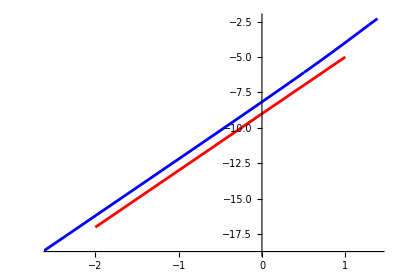

```mathematica
Diff[s_,y_]:=Abs[ResMSbar[MMSbar[MR,m0,mu,y,Γ0],m0,mu,y,Γ0](s-MMSbar[MR,m0,mu,y,Γ0]^2+ⅈ×MMSbar[MR,m0,mu,y,Γ0]GammaMSbar[MR,m0,mu,y,Γ0]+f[s,m0,mu,y])-ResOS[MR,m0,mu,y,Γ0](s-MR^2+ⅈ×MR×Γ0+f[s,m0,mu,y]-Re[f[MR^2-ⅈ×MR×Γ0,m0,mu,y]]-(s-MR^2)Re[fPrime[MR^2-ⅈ×MR×Γ0,m0,mu,y]])];
Show[ParametricPlot[{Log[y],Log[Diff[2,y]]},{y,0.001,4},AspectRatio->0.7,PlotStyle->Blue],Plot[4x-9,{x,-2,1},PlotStyle->Red]]
```

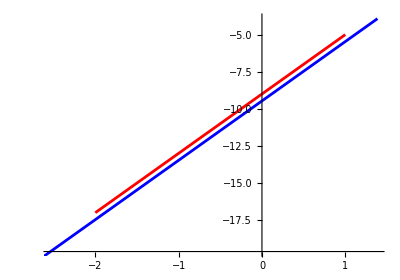

```mathematica
Diff2[s_,y_]:=Abs[ResOS[MR,m0,mu,y,Γ0](s-MR^2+ⅈ×MR×Γ0+f[s,m0,mu,y]-Re[f[MR^2-ⅈ×MR×Γ0,m0,mu,y]]-(s-MR^2)Re[fPrime[MR^2-ⅈ×MR×Γ0,m0,mu,y]])-(s-MPole[MR,m0,mu,y,Γ0]^2+SigmaCOS[s,Sqrt[MR^2-ⅈ MR Γ0],m0,mu,y])];
Show[ParametricPlot[{Log[y],Log[Diff2[2,y]]},{y,0.001,4},AspectRatio->0.7,PlotStyle->Blue],Plot[4x-9,{x,-2,1},PlotStyle->Red]]
```